## Q1:Find the first three roots of the Bessel functionJ_1(x).

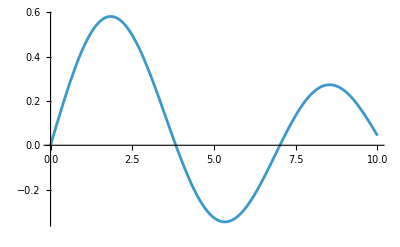

{x→0.}

{x→3.83171}

{x→7.01559}

```mathematica
b1[x_] := BesselJ[1,x];
Plot[b1[x], {x,0,10}]
FindRoot[b1[x], {x,0}]
FindRoot[b1[x], {x,3.5}]
FindRoot[b1[x], {x,7}]
```

## Q2: Integrate the expression f(x) = sin(x) e^-x, and then take its derivative.

```mathematica
f[x_]:= Sin [x] ⅇ^-x
F[x_]:=Integrate[f[x], x]
Integrate[Sin [x] ⅇ^-x, x]
```

-1/2 ⅇ^-x (Cos[x]+Sin[x])

```mathematica
f2= D[F[x],x]
f2
```

-1/2 ⅇ^-x (Cos[x]-Sin[x])+1/2 ⅇ^-x (Cos[x]+Sin[x])

-1/2 ⅇ^-x (Cos[x]-Sin[x])+1/2 ⅇ^-x (Cos[x]+Sin[x])

```mathematica
Simplify[f2[x]]
```

(ⅇ^-x Sin[x])[x]

## Q3: Solve the equation x ln(x) - 3 x + 10 = 6, both symbolically and numerically.

```mathematica
eq = x Log[x]-3x+10 ==6
```

10-3 x+x Log[x]==6

```mathematica
sol = Solve[eq,x, Reals]
```

{{x→ⅇ^(3+ProductLog[-4/ⅇ^3])},{x→ⅇ^(3+ProductLog[-1,-4/ⅇ^3])}}

```mathematica
N[sol,10]
```

{{x→15.52289661},{x→1.568830903}}